```mathematica
f[g_,x_] =1/(4π) (1-g^2)/((1+g^2-2g Cos[x])^(3/2))
```

(1-g^2)/(4 π (1+g^2-2 g Cos[x])^(3/2))

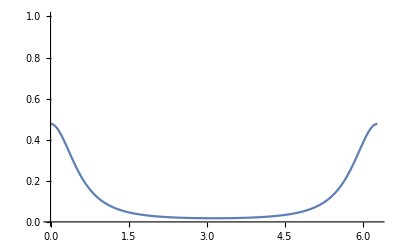

```mathematica
Plot[f[0.5,x], {x,0,2π}, PlotRange->{0,1}]
```

```mathematica
θ = ProbabilityDistribution[f[0.3,x], {x,0,2π}]
```

ProbabilityDistribution[0.0724155/(1.09-0.6 Cos[x])^(3/2),{x,0,2 π}]

```mathematica
ϕ = ProbabilityDistribution[f[0.4,x], {x,0,2π}]
```

ProbabilityDistribution[0.0668451/(1.16-0.8 Cos[x])^(3/2),{x,0,2 π}]

```mathematica
n=10^5
```

100000

```mathematica
thetas = RandomVariate[θ,n];
```

```mathematica
phis = RandomVariate[ϕ,n];
```

```mathematica
T=Table[{Sin[thetas[[k]]]*Cos[phis[[k]]], Sin[thetas[[k]]]*Sin[phis[[k]]], Cos[phis[[k]]]}, {k,n}];
```

```mathematica
ListPointPlot3D[T, AxesLabel->{x,y,z}]
```

-Graphics3D-

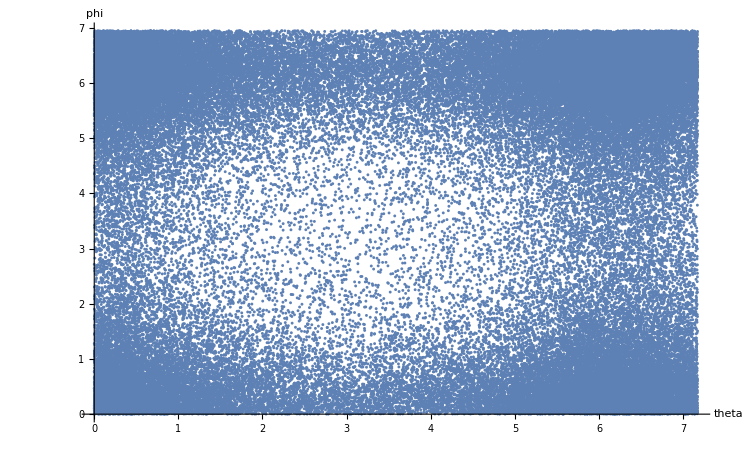

```mathematica
ListPlot[Table[{thetas[[k]], phis[[k]]}, {k,n}], AxesLabel-> {theta, phi}]
```

```mathematica
Max[thetas]
```

7.17236

```mathematica
N[2π]
```

6.28319